## Пучки Лагерра-Гаусса и Эрмита-Гаусса

```mathematica
q[z0_,z_]:=z-ⅈ z0;
w0[z0_,λ_]:=√((λ z0)/π);
w[z0_,λ_,z_]:=w0[z0,λ] √(1+z^2/z0^2);
R[z0_,z_]:=z(1+(z0/z)^2);
ξ[z0_,z_]:=ArcTan[z/z0];

uHG[n_,m_,z0_,λ_, x_, y_, z_]:=(w0[z0,λ]/w[z0,λ,z])HermiteH[n, (√2 x)/w[z0,λ,z]]HermiteH[m, (√2 y)/w[z0,λ,z]]Exp[-1/2((√2 x)/w[z0,λ,z])^2-1/2((√2 y)/w[z0,λ,z])^2]Exp[-ⅈ (2π)/λ z-ⅈ (2π)/λ(x^2+y^2)/(2 R[z0,z])+ⅈ(n+m+1)ξ[z0,z]];
IntensityHG[n_,m_,z0_,λ_, x_, y_, z_]:=((w0[z0,λ]/w[z0,λ,z])HermiteH[n, (√2 x)/w[z0,λ,z]]HermiteH[m, (√2 y)/w[z0,λ,z]]Exp[-1/2((√2 x)/w[z0,λ,z])^2-1/2((√2 y)/w[z0,λ,z])^2])^2;
```

```mathematica
Manipulate[DensityPlot[IntensityHG[m, n, 1, 1, x,y,z],{x,-4,4},{y,-4,4}, PlotRange->All, ColorFunction->GrayLevel],
{{z,0},0,20},
{m,0,5,1},
{n,0,5,1}]
```

```mathematica
Manipulate[Plot[IntensityHG[0, 0, 1, 1, x,0,z],{x,0,10}, 
PlotRange->All,
AxesLabel->{"r", "Intensity"}],
{z, 0, 10}]
```

```mathematica
uLG[l_,m_,z0_,λ_, x_, y_, z_]:=(w0[z0,λ]/w[z0,λ,z])((√(x^2+y^2))/w[z0,λ,z])^l LaguerreL[l,m,(2(x^2+y^2))/w[z0,λ,z]^2]Exp[(-(x^2+y^2))/w[z0,λ,z]^2]Exp[-ⅈ (2π)/λ z-ⅈ (2π)/λ(x^2+y^2)/(2 R[z0,z])-ⅈ l ArcCos[x/(√(x^2+y^2))]+ⅈ(l+2m+1)ξ[z0,z]];
IntensityLG[l_,m_,z0_,λ_, x_, y_, z_]:=(w0[z0,λ]/w[z0,λ,z])((√(x^2+y^2))/w[z0,λ,z])^l LaguerreL[l,m,(2(x^2+y^2))/w[z0,λ,z]^2]Exp[(-(x^2+y^2))/w[z0,λ,z]^2];
Manipulate[DensityPlot[IntensityLG[l, m, 1, 1, x,y,z],{x,-4,4},{y,-4,4}, PlotRange->All, ColorFunction->GrayLevel],{{z,0},0,4},
{l,0,5,1},
{m,0,5,1}]
```

```mathematica
Manipulate[Plot[IntensityLG[1, 1, 1, 1, x,0,z],{x,0,10}, 
PlotRange->All,
AxesLabel->{"r", "Intensity"}],
{z, 0, 10}]
```

## Подгон параметров пучка, тестирование

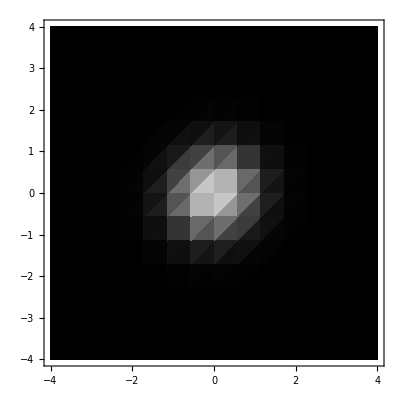

```mathematica
data1=Table[DensityPlot[IntensityHG[0, 0, 1, 1, x,y,z],{x,-4,4},{y,-4,4}, ColorFunction->GrayLevel, PlotRange->All], {z, 2, 8.5, 44.5}]
```

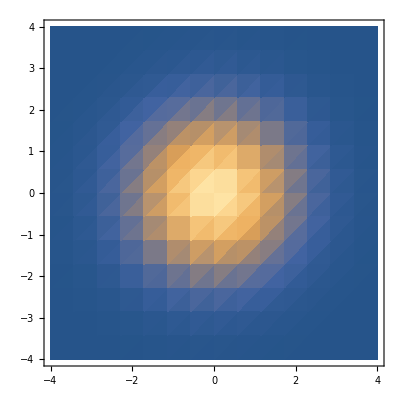
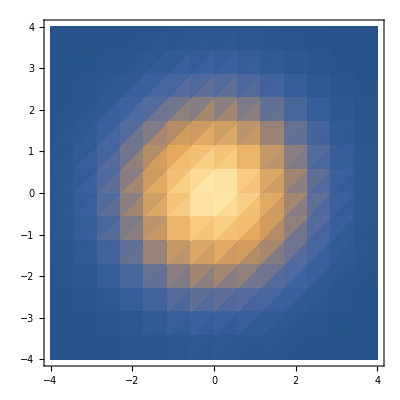
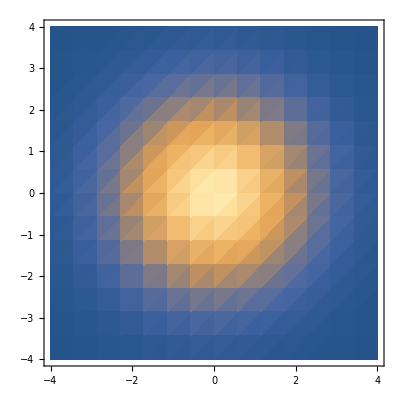
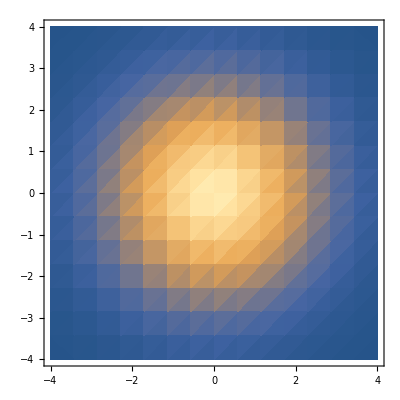
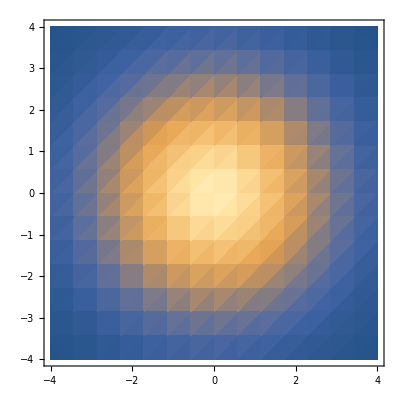
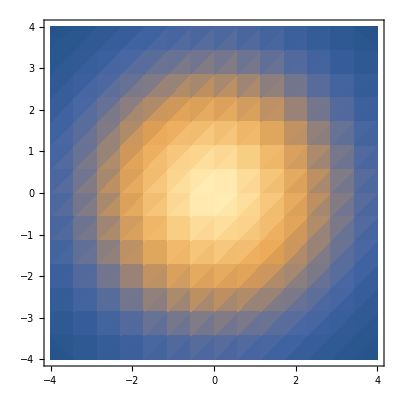
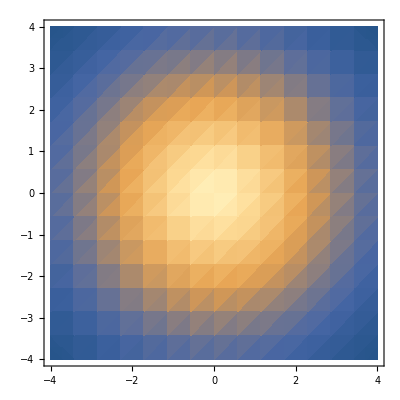
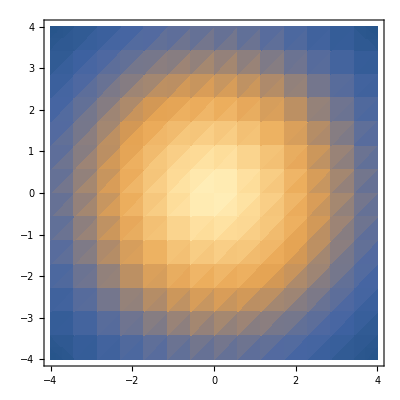

```mathematica
SetDirectory["/Users/goloshch/Desktop/Resonator/data/test_gauss_fit"];
data=Table[{ToString[z]<>".jpg",Show[DensityPlot[IntensityHG[0, 0, 1, 1, x,y,z],{x,-4,4},{y,-4,4}, PlotRange->All, ColorFunction->GrayLevel],Axes->False, Frame->False, PlotRangePadding->0]}, {z, 0, 5.0, 1}];
Export[First[#],Last[#]]&/@data
```

{0.jpg,1.jpg,2.jpg,3.jpg,4.jpg,5.jpg}

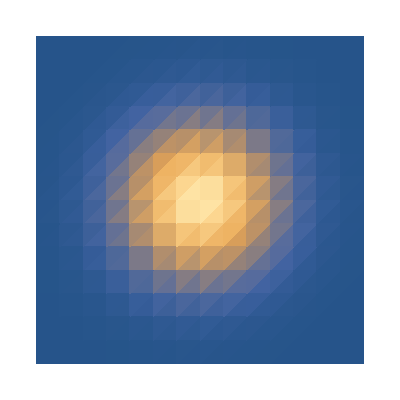
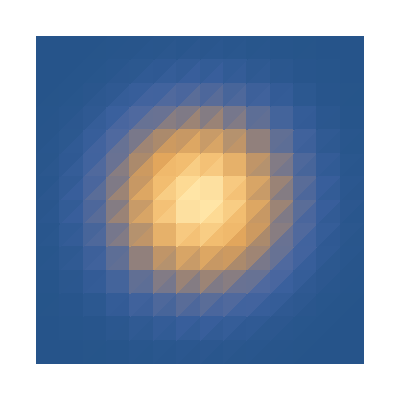
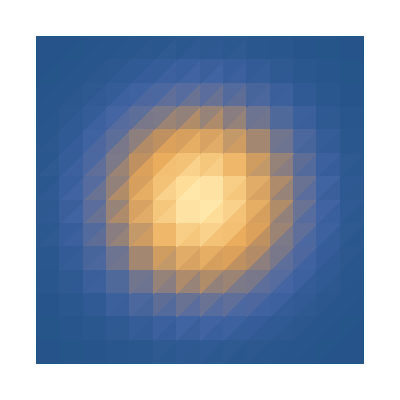
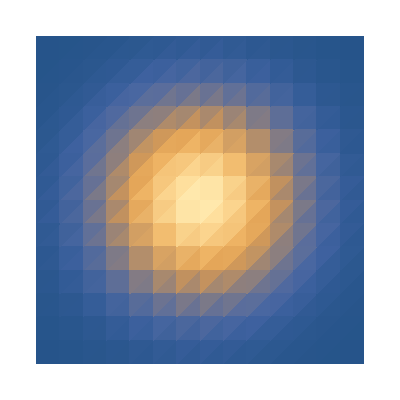
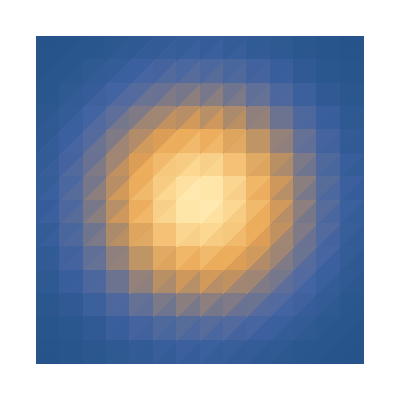
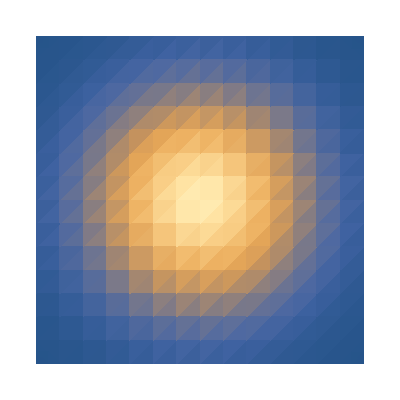
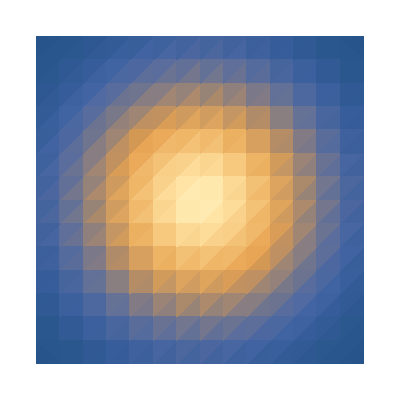
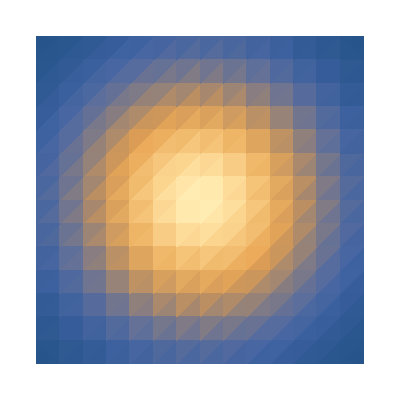

```mathematica
Table[Show[DensityPlot[IntensityHG[0, 0, 2, 1, x,y,z],{x,-4,4},{y,-4,4}, PerformanceGoal->"Quality"], Axes->False, Frame->False], {z, 5.5, 10, 0.5}]
```

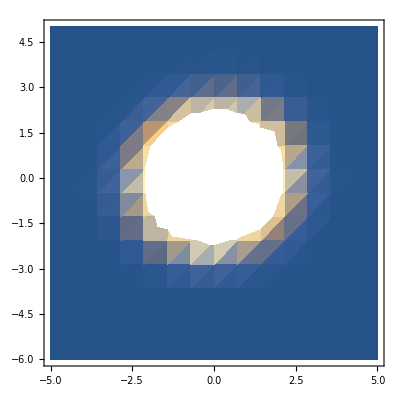
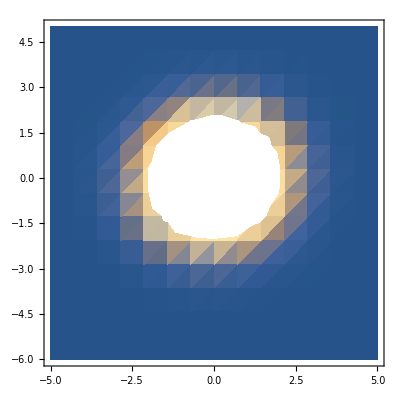
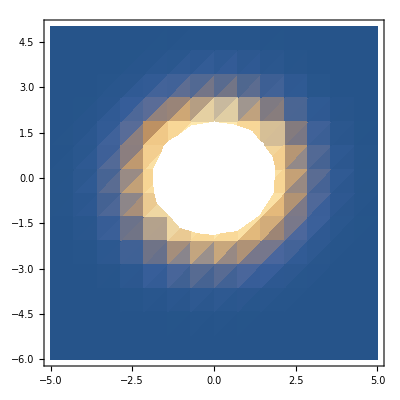
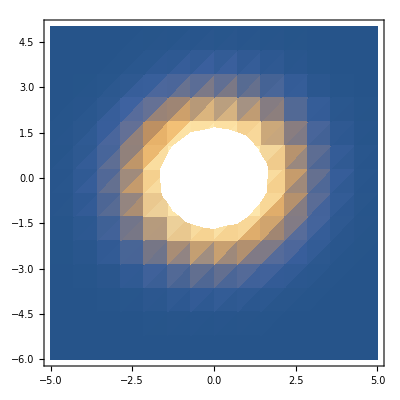
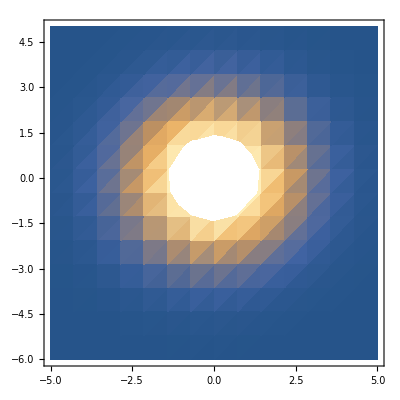
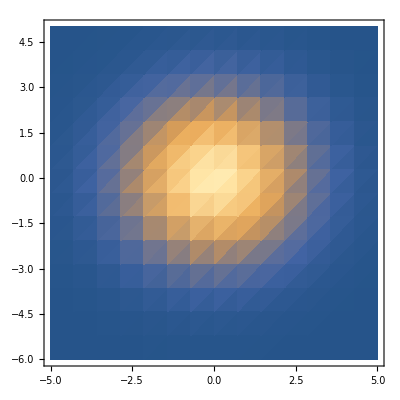
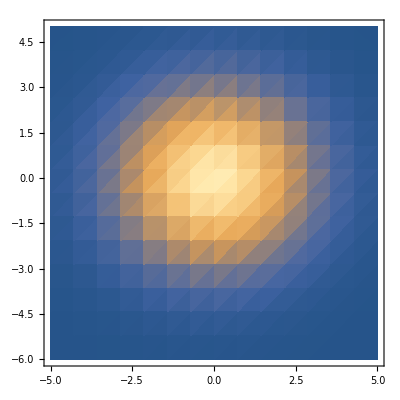
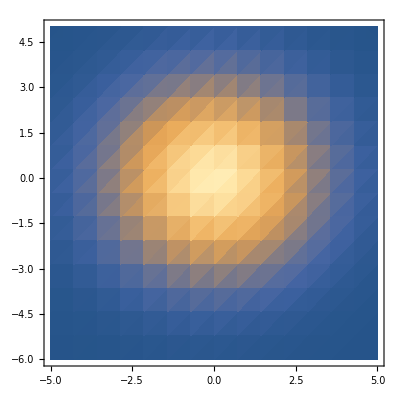

```mathematica
Table[DensityPlot[IntensityHG[0, 0, 0.9, 1, x,y,z],{x,-5,5},{y,-6,5}, PerformanceGoal->"Quality"], {z, 3, 7.5, 0.5}]
```

## Матричная оптика

```mathematica
Manipulate[DensityPlot[Abs[uLG[m, l, 1, 1, x,y,z]]^2,{x,-4,4},{y,-4,4}, PlotRange->All, ColorFunction->GrayLevel, PerformanceGoal->"Quality"],{{z,1},0,4},
{l,0,5,1},
{m,0,5,1}]
```

## Резонатор

```mathematica
c=1;
FSR[L_]:=c/(2 L);
Transmission[r1_,r2_,ω_,L_]:=(r1 r2-1)^2/(1+r1^2 r2^2-2r1 r2 Cos[ω 2 L/c]);
TransmissionGeneral[R1_,R2_,L_, m_,n_,q_]:=(c/(2L))[q+1/π(m+n+1)ArcCos[(1-L/R1)(1-L/R2)]];
```

```mathematica
Manipulate[Plot[Transmission[r1, r2,ω, 5],{ω,0, 3}, PlotRange->All],{{r1,0.9},0.1,1},{{r2,0.9},0.1,1}]
```

```mathematica
Manipulate[DiscretePlot[TransmissionGeneral[R1, R2, 1, 0, m, 1]/(m+1), {m, 0, 5, 1}, PlotRange->All],{R1, 0.5, 2}, {R2, 0.5, 2}]
```

```mathematica
freq=Table[N[TransmissionGeneral[2,2,1,m,0,1]],{m,0,5}]
ms = Table[m, {m, 0, 5}];
data =Transpose@{ms, freq}
ListPlot[data]
```

{0.5[1.41957],0.5[1.83914],0.5[2.25871],0.5[2.67828],0.5[3.09785],0.5[3.51742]}

{{0,0.5[1.41957]},{1,0.5[1.83914]},{2,0.5[2.25871]},{3,0.5[2.67828]},{4,0.5[3.09785]},{5,0.5[3.51742]}}

-Graphics-